```mathematica
Clear["Global`*"]
```

```mathematica
fk[a_,b_,u1_,u2_,α_,β_]:=(a b Sqrt[1+Abs[β]^2] (-2 E^((1+a) Sqrt[α]) (E^u1-E^u2) β ((-1+a) E^(u1+2 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α])+(-1+a) E^(u1+2 b Sqrt[α]) (1+a Sqrt[α]) (1+b Sqrt[α])-2 (-1+a) b E^(u1+(a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α]+(-1+a) E^(u2+2 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β+(-1+a) E^(u2+2 b Sqrt[α]) (1+a Sqrt[α]) (1+b Sqrt[α]) β-2 (-1+a) b E^(u2+(a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β+(-1+a) E^(2 b Sqrt[α]) (1+a Sqrt[α]) (-1+b Sqrt[α]) (1+β)-(-1+a) E^(2 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)+2 (a-b) E^(u1+u2+(a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] (1+β)) Sqrt[α/(1+Abs[β]^2)]+1/(Sqrt[1+Abs[β]^2]) (E^(2 u1+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β+E^(2 u2+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β-E^(2 (u1+(1+a) Sqrt[α])) (-1+a Sqrt[α]) (1+b Sqrt[α]) β-E^(2 (u2+(1+a) Sqrt[α])) (-1+a Sqrt[α]) (1+b Sqrt[α]) β-E^(2 (u1+(1+b) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β-E^(2 (u2+(1+b) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β+E^(2 (u1+(a+b) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β+E^(2 (u2+(a+b) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β+2 b E^(2 u1+(2+a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β-4 b E^(u1+u2+(2+a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β+2 b E^(2 u2+(2+a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β-2 b E^(2 u1+(3 a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β+4 b E^(u1+u2+(3 a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β-2 b E^(2 u2+(3 a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β-E^(u2+2 (1+b) Sqrt[α]) (1+a Sqrt[α]) (-1+b Sqrt[α]) (1+β)+E^(u2+2 (a+b) Sqrt[α]) (1+a Sqrt[α]) (-1+b Sqrt[α]) (1+β)-E^(u2+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)-E^(2 u1+u2+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)+E^(u2+2 (1+a) Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)+E^(2 u1+u2+2 (a+b) Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)-E^(2 u1+u2+2 (1+a) Sqrt[α]) (1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)+E^(2 u1+u2+2 (1+b) Sqrt[α]) (1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)-E^(u1+2 (1+b) Sqrt[α]) (1+a Sqrt[α]) (-1+b Sqrt[α]) β (1+β)+E^(u1+2 (a+b) Sqrt[α]) (1+a Sqrt[α]) (-1+b Sqrt[α]) β (1+β)+E^(u1+2 (u2+(a+b) Sqrt[α])) (-1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)-E^(u1+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)-E^(u1+2 u2+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)+E^(u1+2 (1+a) Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)-E^(u1+2 (u2+(1+a) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)+E^(u1+2 (u2+(1+b) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)+2 E^(u1+u2+2 (1+b) Sqrt[α]) (1+a Sqrt[α]) (-1+(-1+b Sqrt[α]) β-β^2)+2 E^(u1+u2+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β+β^2)+2 E^(u1+u2+2 (1+a) Sqrt[α]) (1+b Sqrt[α]) (1+β+a Sqrt[α] β+β^2)+2 E^(u1+u2+2 (a+b) Sqrt[α]) (1+β-b Sqrt[α] β+β^2+a (-Sqrt[α] β+b α (1+β+β^2))))+β (2 E^((1+a) Sqrt[α]) (E^u1-E^u2) ((-1+a) E^(u1+2 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α])+(-1+a) E^(u1+2 b Sqrt[α]) (1+a Sqrt[α]) (1+b Sqrt[α])-2 (-1+a) b E^(u1+(a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α]+(-1+a) E^(u2+2 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β+(-1+a) E^(u2+2 b Sqrt[α]) (1+a Sqrt[α]) (1+b Sqrt[α]) β-2 (-1+a) b E^(u2+(a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β+(-1+a) E^(2 b Sqrt[α]) (1+a Sqrt[α]) (-1+b Sqrt[α]) (1+β)-(-1+a) E^(2 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)+2 (a-b) E^(u1+u2+(a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] (1+β)) Sqrt[α/(1+Abs[β]^2)]+1/(Sqrt[1+Abs[β]^2]) (E^(2 u1+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β+E^(2 u2+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β-E^(2 (u1+(1+a) Sqrt[α])) (-1+a Sqrt[α]) (1+b Sqrt[α]) β-E^(2 (u2+(1+a) Sqrt[α])) (-1+a Sqrt[α]) (1+b Sqrt[α]) β-E^(2 (u1+(1+b) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β-E^(2 (u2+(1+b) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β+E^(2 (u1+(a+b) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β+E^(2 (u2+(a+b) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β+2 b E^(2 u1+(2+a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β-4 b E^(u1+u2+(2+a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β+2 b E^(2 u2+(2+a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β-2 b E^(2 u1+(3 a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β+4 b E^(u1+u2+(3 a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β-2 b E^(2 u2+(3 a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β-E^(u2+2 (1+b) Sqrt[α]) (1+a Sqrt[α]) (-1+b Sqrt[α]) (1+β)+E^(u2+2 (a+b) Sqrt[α]) (1+a Sqrt[α]) (-1+b Sqrt[α]) (1+β)-E^(u2+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)-E^(2 u1+u2+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)+E^(u2+2 (1+a) Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)+E^(2 u1+u2+2 (a+b) Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)-E^(2 u1+u2+2 (1+a) Sqrt[α]) (1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)+E^(2 u1+u2+2 (1+b) Sqrt[α]) (1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)-E^(u1+2 (1+b) Sqrt[α]) (1+a Sqrt[α]) (-1+b Sqrt[α]) β (1+β)+E^(u1+2 (a+b) Sqrt[α]) (1+a Sqrt[α]) (-1+b Sqrt[α]) β (1+β)+E^(u1+2 (u2+(a+b) Sqrt[α])) (-1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)-E^(u1+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)-E^(u1+2 u2+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)+E^(u1+2 (1+a) Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)-E^(u1+2 (u2+(1+a) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)+E^(u1+2 (u2+(1+b) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)+2 E^(u1+u2+2 (1+b) Sqrt[α]) (1+a Sqrt[α]) (-1+(-1+b Sqrt[α]) β-β^2)+2 E^(u1+u2+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β+β^2)+2 E^(u1+u2+2 (1+a) Sqrt[α]) (1+b Sqrt[α]) (1+β+a Sqrt[α] β+β^2)+2 E^(u1+u2+2 (a+b) Sqrt[α]) (1+β-b Sqrt[α] β+β^2+a (-Sqrt[α] β+b α (1+β+β^2)))))))/((1+β) (-2 a^3 b (E^u1-E^u2)^2 (E^((2+a+b) Sqrt[α])+E^((3 a+b) Sqrt[α])) α β+b (-1+E^u1) (-1+E^u2) (1+β) (E^(u2+2 (a+b) Sqrt[α]) (1-b Sqrt[α])+E^(u2+2 (1+b) Sqrt[α]) (-1+b Sqrt[α])-E^(u2+4 a Sqrt[α]) (1+b Sqrt[α])+E^(u2+2 (1+a) Sqrt[α]) (1+b Sqrt[α])+E^(u1+2 (1+b) Sqrt[α]) (-1+b Sqrt[α]) β-E^(u1+4 a Sqrt[α]) (1+b Sqrt[α]) β+E^(u1+2 (1+a) Sqrt[α]) (1+b Sqrt[α]) β+E^(u1+u2+4 a Sqrt[α]) (1+b Sqrt[α]) (1+β)-E^(u1+u2+2 (1+a) Sqrt[α]) (1+b Sqrt[α]) (1+β)+E^(u1+u2+2 (1+b) Sqrt[α]) (1+b Sqrt[α]) (1+β)-E^(u1+u2+2 (a+b) Sqrt[α]) (1+b Sqrt[α]) (1+β)+E^(u1+2 (a+b) Sqrt[α]) (β-b Sqrt[α] β))+a^2 Sqrt[α] (2 b E^(2 u1+(2+a+b) Sqrt[α]) (-1+Sqrt[α]) β-4 b E^(u1+u2+(2+a+b) Sqrt[α]) (-1+Sqrt[α]) β+2 b E^(2 u2+(2+a+b) Sqrt[α]) (-1+Sqrt[α]) β+2 b E^(2 u1+(3 a+b) Sqrt[α]) (1+Sqrt[α]) β-4 b E^(u1+u2+(3 a+b) Sqrt[α]) (1+Sqrt[α]) β+2 b E^(2 u2+(3 a+b) Sqrt[α]) (1+Sqrt[α]) β-2 b E^(u1+u2+2 (1+a) Sqrt[α]) (1+b Sqrt[α]) β+E^(2 (u1+(1+a) Sqrt[α])) (1+b Sqrt[α]) (-1+b-β) β+E^(2 (u1+(1+b) Sqrt[α])) (-1+b^2 Sqrt[α]+b (-1+Sqrt[α] (-1+β))-β) β-E^(2 (u1+(a+b) Sqrt[α])) (-1-b^2 Sqrt[α]+b (1+Sqrt[α] (-1+β))-β) β-(1+b) E^(u2+2 (1+b) Sqrt[α]) (-1+b Sqrt[α]) (1+β)+(1+b) E^(u2+2 (a+b) Sqrt[α]) (-1+b Sqrt[α]) (1+β)-(1+b) E^(u2+4 a Sqrt[α]) (1+b Sqrt[α]) (1+β)+(1+b) E^(u2+2 (1+a) Sqrt[α]) (1+b Sqrt[α]) (1+β)-(1+b) E^(2 u1+u2+2 (1+a) Sqrt[α]) (1+b Sqrt[α]) (1+β)+E^(2 u1+u2+2 (a+b) Sqrt[α]) (1+b^2 Sqrt[α]+b (1+Sqrt[α] (1-2 β))) (1+β)-(1+b) E^(u1+2 (1+b) Sqrt[α]) (-1+b Sqrt[α]) β (1+β)+(1+b) E^(u1+2 (a+b) Sqrt[α]) (-1+b Sqrt[α]) β (1+β)-(1+b) E^(u1+2 (u2+(1+a) Sqrt[α])) (1+b Sqrt[α]) β (1+β)-(1+b) E^(u1+4 a Sqrt[α]) (1+b Sqrt[α]) β (1+β)+(1+b) E^(u1+2 (1+a) Sqrt[α]) (1+b Sqrt[α]) β (1+β)+E^(2 (u1+u2+2 a Sqrt[α])) (1+b Sqrt[α]) (1+β)^2+E^(2 (u1+u2+(1+a) Sqrt[α])) (1+b Sqrt[α]) (1+β)^2-E^(2 (u1+u2+(1+b) Sqrt[α])) (1+b Sqrt[α]) (1+β)^2-E^(2 (u1+u2+(a+b) Sqrt[α])) (1+b Sqrt[α]) (1+β)^2+E^(2 u1+4 a Sqrt[α]) (1+b Sqrt[α]) β (1+b+β)-E^(2 u1+u2+4 a Sqrt[α]) (1+b Sqrt[α]) (1+β) (1+b+2 β)+E^(2 u1+u2+2 (1+b) Sqrt[α]) (1+β) (1+b+b Sqrt[α]+b^2 Sqrt[α]+2 β)+E^(2 (u2+(1+a) Sqrt[α])) (1+b Sqrt[α]) (-1+(-1+b) β)+E^(2 u2+4 a Sqrt[α]) (1+b Sqrt[α]) (1+β+b β)-E^(u1+2 u2+4 a Sqrt[α]) (1+b Sqrt[α]) (1+β) (2+β+b β)+E^(u1+2 (u2+(1+b) Sqrt[α])) (1+β) (2+(1+b) (1+b Sqrt[α]) β)+E^(2 (u2+(a+b) Sqrt[α])) (1+b (Sqrt[α] (-1+β)-β)+β+b^2 Sqrt[α] β)+E^(u1+2 (u2+(a+b) Sqrt[α])) (1+β) (β+b^2 Sqrt[α] β+b (Sqrt[α] (-2+β)+β))+E^(2 (u2+(1+b) Sqrt[α])) (-1-β+b^2 Sqrt[α] β-b (Sqrt[α] (-1+β)+β))+2 E^(u1+u2+4 a Sqrt[α]) (1+b Sqrt[α]) ((1+β)^2+b (1+β+β^2))-2 E^(u1+u2+2 (1+b) Sqrt[α]) (b^2 Sqrt[α] β+(1+β)^2+b (1+β-2 Sqrt[α] β+β^2))+2 b E^(u1+u2+2 (a+b) Sqrt[α]) (β+Sqrt[α] (1+β^2+b (1+β+β^2))))-a (E^(2 (u2+(1+a) Sqrt[α])) (1+b Sqrt[α]) (-1+b (Sqrt[α] (-1+β)-β)-β)-2 b E^(2 u1+(2+a+b) Sqrt[α]) (2+b Sqrt[α]) Sqrt[α] β+4 b E^(u1+u2+(2+a+b) Sqrt[α]) (2+b Sqrt[α]) Sqrt[α] β-2 b E^(2 u2+(2+a+b) Sqrt[α]) (2+b Sqrt[α]) Sqrt[α] β+2 b E^(2 u1+(3 a+b) Sqrt[α]) (2+b Sqrt[α]) Sqrt[α] β-4 b E^(u1+u2+(3 a+b) Sqrt[α]) (2+b Sqrt[α]) Sqrt[α] β+2 b E^(2 u2+(3 a+b) Sqrt[α]) (2+b Sqrt[α]) Sqrt[α] β-E^(u2+2 (1+b) Sqrt[α]) (1+b-2 b Sqrt[α]+b^2 (-Sqrt[α]+α)) (1+β)+E^(u2+2 (a+b) Sqrt[α]) (1+b-2 b Sqrt[α]+b^2 (-Sqrt[α]+α)) (1+β)-E^(u2+4 a Sqrt[α]) (1+b+2 b Sqrt[α]+b^2 (Sqrt[α]+α)) (1+β)+E^(u2+2 (1+a) Sqrt[α]) (1+b+2 b Sqrt[α]+b^2 (Sqrt[α]+α)) (1+β)-E^(u1+2 (1+b) Sqrt[α]) (1+b-2 b Sqrt[α]+b^2 (-Sqrt[α]+α)) β (1+β)+E^(u1+2 (a+b) Sqrt[α]) (1+b-2 b Sqrt[α]+b^2 (-Sqrt[α]+α)) β (1+β)-E^(u1+4 a Sqrt[α]) (1+b+2 b Sqrt[α]+b^2 (Sqrt[α]+α)) β (1+β)+E^(u1+2 (1+a) Sqrt[α]) (1+b+2 b Sqrt[α]+b^2 (Sqrt[α]+α)) β (1+β)+E^(2 (u1+u2+2 a Sqrt[α])) (1+b Sqrt[α])^2 (1+β)^2-E^(2 (u1+u2+(a+b) Sqrt[α])) (1+b Sqrt[α])^2 (1+β)^2+E^(2 (u1+u2+(1+a) Sqrt[α])) (-1+b^2 α) (1+β)^2-E^(2 (u1+u2+(1+b) Sqrt[α])) (-1+b^2 α) (1+β)^2-E^(2 (u1+(1+a) Sqrt[α])) (1+b Sqrt[α]) β (1+b (1+Sqrt[α] (-1+β))+β)-E^(2 (u1+(a+b) Sqrt[α])) β (1+b (1-2 Sqrt[α] (-1+β))+b^2 (-Sqrt[α]+α (-1+β))+β)+E^(2 u1+u2+2 (1+a) Sqrt[α]) (1+b Sqrt[α]) (1+β) (1+b-b Sqrt[α]+2 β)-E^(u1+2 (u2+(1+a) Sqrt[α])) (1+b Sqrt[α]) (1+β) (-2+(-1+b (-1+Sqrt[α])) β)+E^(u1+2 (u2+(1+b) Sqrt[α])) (1+β) (-2+b (2 Sqrt[α]-β)-β+b^2 (-Sqrt[α]+α) β)+E^(u1+2 (u2+(a+b) Sqrt[α])) (1+b Sqrt[α]) (1+β) (2+β+b (Sqrt[α] (-2+β)+β))+E^(2 (u2+(a+b) Sqrt[α])) (-1-β-b (2 Sqrt[α] (-1+β)+β)+b^2 (α (-1+β)+Sqrt[α] β))+E^(2 u1+u2+2 (1+b) Sqrt[α]) (1+β) (-1+b^2 (-Sqrt[α]+α)-2 β+b (-1+2 Sqrt[α] β))+E^(2 (u1+(1+b) Sqrt[α])) β (1+b+β-2 b Sqrt[α] β+b^2 (-Sqrt[α]+α+α β))+E^(2 (u2+(1+b) Sqrt[α])) (1+β+b (-2 Sqrt[α]+β)+b^2 (α-Sqrt[α] β+α β))-2 E^(u1+u2+2 (1+a) Sqrt[α]) (1+b Sqrt[α]) ((1+β)^2+b (1+β+2 Sqrt[α] β+β^2))+2 E^(u1+u2+2 (a+b) Sqrt[α]) (-(1+β)^2-b (1+β-4 Sqrt[α] β+β^2)+b^2 (α-Sqrt[α] β+α β^2))+E^(2 u1+4 a Sqrt[α]) (1+b Sqrt[α]) β (1+β+b (1+Sqrt[α] (1+β)))+E^(2 u2+4 a Sqrt[α]) (1+b Sqrt[α]) (1+β+b (β+Sqrt[α] (1+β)))+2 E^(u1+u2+4 a Sqrt[α]) (1+b Sqrt[α]) ((1+β)^2+b (1+β+β^2+Sqrt[α] (1+β)^2))-E^(u1+2 u2+4 a Sqrt[α]) (1+b Sqrt[α]) (1+β) (2+β+b (β+Sqrt[α] (2+β)))-E^(2 u1+u2+2 (a+b) Sqrt[α]) (1+b Sqrt[α]) (1+β) (-1-2 β+b (-1+Sqrt[α] (-1+2 β)))-E^(2 u1+u2+4 a Sqrt[α]) (1+b Sqrt[α]) (1+β) (1+2 β+b (1+Sqrt[α] (1+2 β)))+2 E^(u1+u2+2 (1+b) Sqrt[α]) (b^2 Sqrt[α] β+(1+β)^2+b (1+β+β^2-Sqrt[α] (1+4 β+β^2))))))
```

```mathematica
d=1;
U01=4;
U02=0;
a=3;
b=1;
nmin=4;
nmax=6;
npoints=nmax-nmin+1;
Rsink=1;
Rmax=25;
t0=0;
t1=1000;
rdmin=-2;
rdmax=3;
datapoints =12;
u1[r_]:=U01 Exp[-((r-a)/b)^n];
u2[r_]:=U02 Exp[-((r-a)/b)^n];
pde = {D[ρ1[r,t],t]==2/r ρ1[r,t] u1'[r]+D[ρ1[r,t],r]u1'[r]+ρ1[r,t] u1''[r]+d 2/r D[ρ1[r,t],r]+d D[ρ1[r,t],r,r]-w12 ρ1[r,t] + w21 ρ2[r,t],
D[ρ2[r,t],t]==2/r ρ2[r,t] u2'[r]+D[ρ2[r,t],r]u2'[r]+ρ2[r,t] u2''[r]+d 2/r D[ρ2[r,t],r]+d D[ρ2[r,t],r,r]-w21 ρ2[r,t] + w12 ρ1[r,t]
};
bc = {
ρ1[Rsink,t]==0,
ρ2[Rsink,t]==0,
ρ1[Rmax,t]==w21/(w12+w21),
ρ2[Rmax,t]==w12/(w12+w21)
};
ic = {
ρ1[r,t0]==w21/(w12+w21)*(1-1/r),
ρ2[r,t0]==w12/(w12+w21)*(1-1/r)
};
```

```mathematica
Densities=Table[0,{k,1,3},{i,1,datapoints+1},{j,1,npoints+1}];
ReactionRate=Table[0,{k,1,2},{i,1,datapoints+1},{j,1,npoints+1}];
```

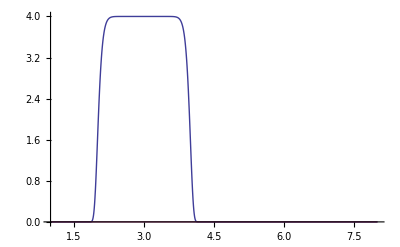

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

Donen=16i=0w12=0.00005

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

Donen=16i=1w12=0.000340646

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

General::stop: Further output of NDSolve :: ibcinc will be suppressed during this calculation.

Donen=16i=2w12=0.00232079

Donen=16i=3w12=0.0158114

Donen=16i=4w12=0.107722

$Aborted

```mathematica
For[j=0,j≤npoints,j++,
n=2^(nmin+j);
Print[Plot[{u1[r],u2[r]},{r,Rsink,8},PlotRange->All]];
For[i=0,i<=datapoints,i++,
rd=10^(rdmin+i*(rdmax-rdmin)/datapoints);
w21=d*rd^2/2;
w12=w21;
sol=NDSolve[{pde,bc,ic},{ρ1,ρ2},{t,t1,t1},{r,Rsink,Rmax},MaxSteps->Infinity,MaxStepFraction->0.002,AccuracyGoal->15,StartingStepSize->0.001,WorkingPrecision->MachinePrecision,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->24000}}];
Print["Done","n=",n,"i=",i,"w12=",N[w12]];
ρ1eq[r_]=ρ1[r,t1]/.sol;
ρ2eq[r_]=ρ2[r,t1]/.sol;
ρtot[r_]=(ρ1[r,t1]+ρ2[r,t1])/.sol;

Densities[[1,i+1,j+1]]=ρ1eq[r];
Densities[[2,i+1,j+1]]=ρ2eq[r];
Densities[[3,i+1,j+1]]=ρtot[r];
ReactionRate[[1,i+1,j+1]]=w12;
ReactionRate[[2,i+1,j+1]]=D[ρtot[r],r]/.r->1;
]]
```

```mathematica
b=Table[0,{i,1,npoints+1}];
b[[1]]=N[ReactionRate[[1,All,1]]];
For[j=1,j≤npoints,j++,
b[[j+1]]=N[0.945901*Flatten[ReactionRate[[2,All,j]]]];
]
Export["numeric_rates.csv",Transpose[b]];
```

```mathematica
resolution=10
c=Table[0,{i,0,npoints+2},{j,1,resolution}];
c[[1;;2,All]]
c[[1;;2,All]]=Table[{N[10^rd],fk[at,bt,U01,U02,10^(rd)^2*d,1]},{rd,rdmin,rdmax,(rdmax-rdmin)/resolution}];
Export["analytic_rates.csv",N[c]]
For[j=0,j≤npoints,j++,
n=2^(nmin+j);
k=Integrate[Exp[u1[r]/2]/(r^2),{r,1,Infinity}]^(-1)
Print[n,k]
]
```

10

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

analytic_rates.csv

16 1/(∫_1^∞ (ⅇ^(2 ⅇ^(-(-3+r)^32)))/r^2 ⅆr)

32 Null/(∫_1^∞ (ⅇ^(2 ⅇ^(-(-3+r)^16)))/r^2 ⅆr)

$Aborted

```mathematica
n=2;
Integrate[Exp[u1[r]/2]/(r^2),{r,1,Infinity}]
```

∫_1^∞ (ⅇ^(2 ⅇ^(-(-3+r)^2)))/r^2 ⅆr

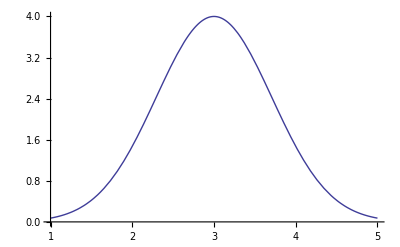

```mathematica
Plot[u1[r],{r,1,5}]
```

```mathematica
c1={ReactionRate[[1]],Flatten[ReactionRate[[2,All,1]]]};
c2={ReactionRate[[1]],Flatten[ReactionRate[[2,All,2]]]};
c3={ReactionRate[[1]],Flatten[ReactionRate[[2,All,3]]]};
```

Part::partw: Part 2 of {0.574846} does not exist.

Part::partw: Part 3 of {0.574846} does not exist.

```mathematica
ReactionRate
npoints
```

{{1/20000[1/20000,1/20000],1/(200 10^(1/3))[1/(200 10^(1/3)),1/(200 10^(1/3))],1/(2 10^(2/3))[1/(2 10^(2/3)),1/(2 10^(2/3))],5[5,5],(50 10^(2/3))[50 10^(2/3),50 10^(2/3)],(5000 10^(1/3))[5000 10^(1/3),5000 10^(1/3)],500000[500000,500000]},{{0.560402}[{0.560402},{0.560402}],{0.560402}[{0.560402},{0.560402}],{0.560402}[{0.560402},{0.560402}],{0.560402}[{0.560402},{0.560402}],{0.560402}[{0.560402},{0.560402}],{0.560402}[{0.560402},{0.560402}],{0.560402}[{0.560402},{0.560402}]}}

2

```mathematica
Plot[Densities[[All, 3,1]],{r,1,6}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol :: argx will be suppressed during this calculation.

-Graphics-